```mathematica
Multi[v1_,v2_]:=Table[v1[[k]]*v2[[k]],{k,Length[v1]}]
```

```mathematica
Clear[MyVectors];MyVectors[x_]:=MyVectors[x]=Block[{result=Association[],vec},
Table[
vect=BaseCoeff4[k,"C"];
result[vect]=k;
,{k,Keys[allGraphs4]}];
result
]
```

```mathematica
MyVectors[1]
```

<|{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}→0,{1,0,1,1,1,1,1,0,0,0,1,1,1,1,0}→243,{1,0,0,1,1,1,1,0,0,0,0,0,1,1,0}→324,{1,0,0,0,1,1,1,0,0,0,0,0,0,1,0}→351,{1,0,0,0,0,1,1,0,0,0,0,0,0,0,0}→360,{1,0,0,0,0,0,1,0,0,0,0,0,0,0,0}→363,{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0}→364,{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0}→365,{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0}→367,{1,0,0,0,0,1,0,0,0,0,0,0,0,0,0}→361,{0,0,0,0,1,0,0,0,0,0,0,0,0,1,0}→369,{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0}→373,{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0}→377,{1,0,0,0,1,0,1,0,0,0,0,0,0,0,0}→354,{1,0,0,0,1,0,0,0,0,0,0,0,0,0,0}→355,{0,0,0,0,0,1,0,0,0,0,0,0,0,1,0}→357,{1,0,0,0,1,1,0,0,0,0,0,0,0,0,0}→352,{0,0,0,0,0,0,1,0,0,0,0,0,0,1,0}→353,{0,0,0,1,0,0,0,0,0,0,0,0,1,0,0}→382,{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0}→391,{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0}→400,{1,0,0,1,0,1,1,0,0,0,0,0,0,0,0}→333,{1,0,0,1,0,0,1,0,0,0,0,0,0,0,0}→336,{1,0,0,1,0,0,0,0,0,0,0,0,0,0,0}→337,{1,0,0,1,0,1,0,0,0,0,0,0,0,0,0}→334,{0,0,0,0,1,0,0,0,0,0,0,0,1,1,0}→342,{0,0,0,0,1,0,0,0,0,0,0,0,1,0,0}→346,{1,0,0,1,1,0,1,0,0,0,0,0,1,0,0}→327,{1,0,0,1,1,0,0,0,0,0,0,0,1,0,0}→328,{1,0,0,1,1,1,0,0,0,0,0,0,1,0,0}→325,{0,0,1,0,0,0,0,0,0,0,1,1,0,0,0}→414,{0,0,1,0,0,0,0,0,0,0,0,1,0,0,0}→442,{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0}→445,{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0}→448,{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0}→473,{0,0,1,0,0,0,0,0,0,0,1,0,0,0,0}→417,{1,0,1,0,1,1,1,0,0,0,0,1,0,1,0}→270,{1,0,1,0,0,1,1,0,0,0,0,1,0,0,0}→279,{1,0,1,0,0,0,1,0,0,0,0,0,0,0,0}→282,{1,0,1,0,0,0,0,0,0,0,0,0,0,0,0}→283,{0,0,0,0,0,1,0,0,0,0,0,1,0,0,0}→286,{1,0,1,0,0,1,0,0,0,0,0,1,0,0,0}→280,{1,0,1,0,1,0,1,0,0,0,0,0,0,0,0}→273,{1,0,1,0,1,0,0,0,0,0,0,0,0,0,0}→274,{0,0,0,0,0,1,0,0,0,0,0,1,0,1,0}→276,{1,0,1,0,1,1,0,0,0,0,0,1,0,0,0}→271,{0,0,0,1,0,0,0,0,0,0,1,0,1,0,0}→300,{0,0,0,1,0,0,0,0,0,0,1,0,0,0,0}→309,{1,0,1,1,0,1,1,0,0,0,1,1,0,0,0}→252,{1,0,1,1,0,0,1,0,0,0,1,0,0,0,0}→255,{1,0,1,1,0,0,0,0,0,0,0,0,0,0,0}→256,{0,0,0,0,0,0,1,0,0,0,1,0,0,0,0}→257,{1,0,1,1,0,1,0,0,0,0,0,1,0,0,0}→253,{1,0,1,1,1,0,1,0,0,0,1,0,1,0,0}→246,{1,0,1,1,1,0,0,0,0,0,0,0,1,0,0}→247,{1,0,1,1,1,1,0,0,0,0,0,1,1,0,0}→244,{0,0,0,0,0,0,1,0,0,0,1,0,0,1,0}→245,{0,1,0,0,0,0,0,1,1,1,0,0,0,0,1}→486,{0,1,0,0,0,0,0,0,1,1,0,0,0,0,0}→576,{0,1,0,0,0,0,0,0,0,1,0,0,0,0,0}→606,{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0}→607,{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0}→608,{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0}→637,{0,1,0,0,0,0,0,0,1,0,0,0,0,0,0}→577,{0,0,0,0,0,0,0,1,0,0,0,0,0,0,1}→666,{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0}→697,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}→728,{0,1,0,0,0,0,0,1,0,1,0,0,0,0,0}→516,{0,1,0,0,0,0,0,1,0,0,0,0,0,0,0}→517,{0,0,0,0,0,0,0,0,1,0,0,0,0,0,1}→546,{0,1,0,0,0,0,0,1,1,0,0,0,0,0,0}→487,{0,0,0,0,0,0,0,0,0,1,0,0,0,0,1}→488,{1,1,0,1,1,1,1,0,1,1,0,0,1,1,0}→81,{1,1,0,0,1,1,1,0,0,1,0,0,0,1,0}→108,{1,1,0,0,0,1,1,0,0,1,0,0,0,0,0}→117,{1,1,0,0,0,0,1,0,0,1,0,0,0,0,0}→120,{1,1,0,0,0,0,0,0,0,0,0,0,0,0,0}→121,{0,0,0,0,0,0,1,0,0,1,0,0,0,0,0}→122,{1,1,0,0,0,1,0,0,0,0,0,0,0,0,0}→118,{1,1,0,0,1,0,1,0,0,1,0,0,0,0,0}→111,{1,1,0,0,1,0,0,0,0,0,0,0,0,0,0}→112,{1,1,0,0,1,1,0,0,0,0,0,0,0,0,0}→109,{0,0,0,0,0,0,1,0,0,1,0,0,0,1,0}→110,{0,0,0,1,0,0,0,0,1,0,0,0,1,0,0}→136,{0,0,0,1,0,0,0,0,1,0,0,0,0,0,0}→145,{1,1,0,1,0,1,1,0,1,1,0,0,0,0,0}→90,{1,1,0,1,0,0,1,0,0,1,0,0,0,0,0}→93,{1,1,0,1,0,0,0,0,0,0,0,0,0,0,0}→94,{0,0,0,0,0,1,0,0,1,0,0,0,0,0,0}→97,{1,1,0,1,0,1,0,0,1,0,0,0,0,0,0}→91,{1,1,0,1,1,0,1,0,0,1,0,0,1,0,0}→84,{1,1,0,1,1,0,0,0,0,0,0,0,1,0,0}→85,{0,0,0,0,0,1,0,0,1,0,0,0,0,1,0}→87,{1,1,0,1,1,1,0,0,1,0,0,0,1,0,0}→82,{0,0,1,0,0,0,0,1,0,0,1,1,0,0,1}→162,{0,0,1,0,0,0,0,1,0,0,0,1,0,0,0}→190,{0,0,1,0,0,0,0,1,0,0,0,0,0,0,0}→193,{0,0,0,0,0,0,0,0,0,0,1,0,0,0,1}→218,{0,0,1,0,0,0,0,1,0,0,1,0,0,0,0}→165,{0,0,0,0,0,0,0,0,0,0,0,1,0,0,1}→168,{1,1,1,0,1,1,1,1,0,1,0,1,0,1,0}→27,{1,1,1,0,0,1,1,0,0,1,0,1,0,0,0}→36,{1,1,1,0,0,0,1,0,0,1,0,0,0,0,0}→39,{1,1,1,0,0,0,0,0,0,0,0,0,0,0,0}→40,{1,1,1,0,0,1,0,0,0,0,0,1,0,0,0}→37,{0,0,0,0,1,0,0,1,0,0,0,0,0,1,0}→45,{0,0,0,0,1,0,0,1,0,0,0,0,0,0,0}→49,{1,1,1,0,1,0,1,1,0,1,0,0,0,0,0}→30,{1,1,1,0,1,0,0,1,0,0,0,0,0,0,0}→31,{1,1,1,0,1,1,0,1,0,0,0,1,0,0,0}→28,{0,0,0,1,0,0,0,0,1,0,1,0,1,0,1}→54,{0,0,0,1,0,0,0,0,1,0,1,0,0,0,0}→63,{0,0,0,0,0,0,0,0,0,0,0,0,1,0,1}→72,{1,1,1,1,0,1,1,0,1,1,1,1,0,0,0}→9,{1,1,1,1,0,0,1,0,0,1,1,0,0,0,0}→12,{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0}→13,{0,0,0,0,0,0,1,0,0,1,1,0,0,0,0}→14,{0,0,0,0,0,1,0,0,1,0,0,1,0,0,0}→16,{1,1,1,1,0,1,0,0,1,0,0,1,0,0,0}→10,{0,0,0,0,1,0,0,1,0,0,0,0,1,1,1}→18,{0,0,0,0,1,0,0,1,0,0,0,0,1,0,0}→22,{0,0,0,0,0,0,0,0,0,0,0,0,0,1,1}→26,{1,1,1,1,1,0,1,1,0,1,1,0,1,0,0}→3,{1,1,1,1,1,0,0,1,0,0,0,0,1,0,0}→4,{0,0,0,0,0,1,0,0,1,0,0,1,0,1,1}→6,{1,1,1,1,1,1,0,1,1,0,0,1,1,0,0}→1,{0,0,0,0,0,0,1,0,0,1,1,0,0,1,1}→2|>

```mathematica
Block[{vec1,vec2,prod,all=MyVectors[1]
,keys=Select[Keys[allGraphs4],#≠0&]},
Table[
vec1=BaseCoeff4[k,"C"];
Table[
vec2=BaseCoeff4[l,"C"];
prod=Multi[vec1,vec2];
If[KeyExistsQ[all,prod],
{k,l}->all[prod],
NO
]
,{l,keys}]
,{k,keys}]
]
```

{{If[243≠{1,0,1,1,1,1,1,0,0,0,1,1,1,1,0}&&243≠{1,0,1,1,1,1,1,0,0,0,1,1,1,1,0},{k,l}→all[prod],NO],If[324≠{1,0,1,1,1,1,1,0,0,0,1,1,1,1,0}&&324≠{1,0,0,1,1,1,1,0,0,0,0,0,1,1,0},{k,l}→all[prod],NO],If[351≠{1,0,1,1,1,1,1,0,0,0,1,1,1,1,0}&&351≠{1,0,0,0,1,1,1,0,0,0,0,0,0,1,0},{k,l}→all[prod],NO],If[360≠{1,0,1,1,1,1,1,0,0,0,1,1,1,1,0}&&360≠{1,0,0,0,0,1,1,0,0,0,0,0,0,0,0},{k,l}→all[prod],NO],If[363≠{1,0,1,1,1,1,1,0,0,0,1,1,1,1,0}&&363≠{1,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{k,l}→all[prod],NO],117,If[247≠{1,0,1,1,1,1,1,0,0,0,1,1,1,1,0}&&247≠{1,1,1,1,1,0,0,1,0,0,0,0,1,0,0},{k,l}→all[prod],NO],If[276≠{1,0,1,1,1,1,1,0,0,0,1,1,1,1,0}&&276≠{0,0,0,0,0,1,0,0,1,0,0,1,0,1,1},{k,l}→all[prod],NO],If[244≠{1,0,1,1,1,1,1,0,0,0,1,1,1,1,0}&&244≠{1,1,1,1,1,1,0,1,1,0,0,1,1,0,0},{k,l}→all[prod],NO],If[245≠{1,0,1,1,1,1,1,0,0,0,1,1,1,1,0}&&245≠{0,0,0,0,0,0,1,0,0,1,1,0,0,1,1},{k,l}→all[prod],NO]},124,{1}}
 |  |  |  |

```mathematica
jake=Block[{vec1,vec2,prod,all=MyVectors[1]
,keys=Select[Keys[allGraphs4],#≠0&]},
Table[
vec1=BaseCoeff4[k,"C"];
Table[
vec2=BaseCoeff4[l,"C"];
prod=Multi[vec1,vec2];
If[KeyExistsQ[all,prod],
1,
0
]
,{l,keys}]
,{k,keys}]
]
```

{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},123,{1,1,1,1,1,0,1,0,0,1,0,1,1,0,1,0,1,0,0,0,1,1,0,0,1,0,1,0,0,1,0,0,0,1,1,1,1,1,0,0,0,1,0,1,0,1,1,1,1,0,1,0,1,0,0,1,1,1,1,0,1,0,0,1,0,1,1,0,1,0,1,1,1,1,1,0,1,0,1,0,0,1,0,0,1,1,0,0,0,1,0,1,0,1,0,0,1,1,1,1,1,1,0,0,1,0,1,0,0,1,1,1,1,1,0,1,0,0,1,0,1,1,0,1,0,1}}
 |  |  |  |

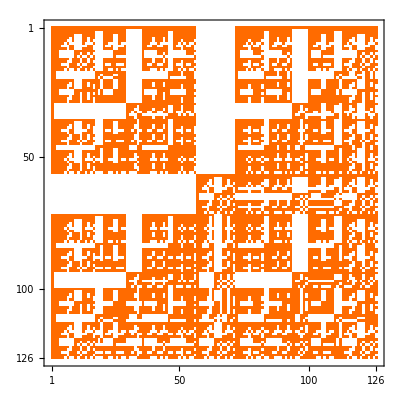

```mathematica
MatrixPlot[jake]
```

```mathematica
PseudoInverse[jake]//MatrixPlot
```

$Aborted

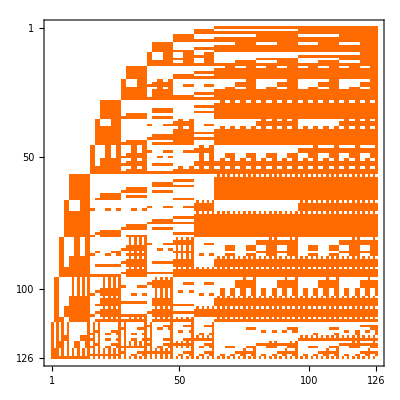

```mathematica
Sort[Transpose[Sort[Transpose[jake]]]]//MatrixPlot
```

```mathematica
jake2=Block[{vec1,vec2,prod,all=MyVectors[1]
,keys=allGraphs5FakeAtomKeys,keys2=allGraphs5NullAtomKeys},
Table[
vec1=BaseCoeff4[k,"C"];
Table[
vec2=BaseCoeff4[l,"C"];
prod=Multi[vec1,vec2];
If[KeyExistsQ[all,prod],
1,
0
]
,{l,keys}]
,{k,keys2}]
]; Total[Flatten[jake2]]
```

113

```mathematica
jake2=Block[{vec1,vec2,prod,all=MyVectors[1]
,keys=allGraphs5FakeAtomKeys,keys2=allGraphs5GeneratorAtomKeys},
Table[
vec1=BaseCoeff4[k,"C"];
Table[
vec2=BaseCoeff4[l,"C"];
prod=Multi[vec1,vec2];
If[KeyExistsQ[all,prod],
1,
0
]
,{l,keys}]
,{k,keys2}]
]; Total[Flatten[jake2]]
```

15

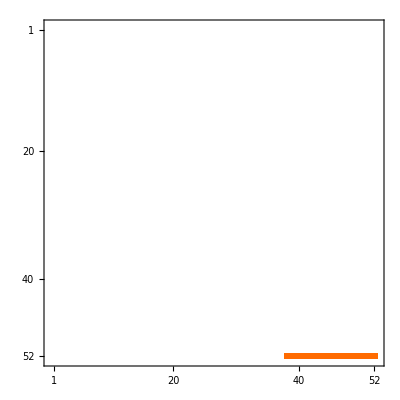

```mathematica
Sort[Transpose[Sort[Transpose[jake2]]]]//MatrixPlot
```